## Convert Covid-19 Cases

```mathematica
path0=NotebookDirectory[];
coviddata=Import[path0<>"covid.csv","CSV"];
days=DayCount[coviddata[[2,4]],coviddata[[-1,4]]]
cases=coviddata[[2;;,6]];
death=coviddata[[2;;,9]];
```

697

```mathematica
avgcase=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@cases[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
avgdeath=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@death[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
Export[path0<>"cases.csv",{avgcase},"CSV"];
Export[path0<>"casesD.csv",{avgdeath*1/0.0037},"CSV"];
```

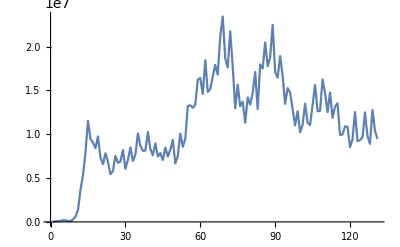

```mathematica
ListPlot[avgdeath*1/0.0037,Joined->True]
```

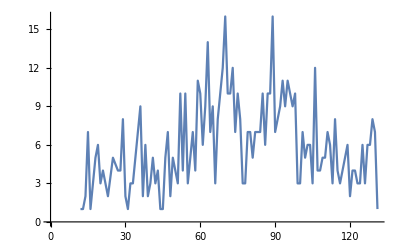

```mathematica
path0=NotebookDirectory[];
cases=Import[path0<>"casesD.csv","CSV"][[1]];
Table[{i,RandomVariate[BinomialDistribution[Floor@cases[[i]],5*10^-7],1][[1]]},{i,1,Length[cases]}];
data=Select[%,#[[2]]>0&];
ListPlot[data,Joined->True]
```

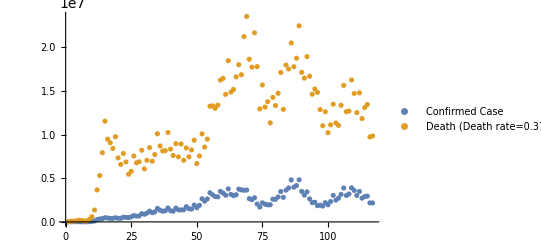

```mathematica
ListPlot[{avgcase,1/0.0037*avgdeath},PlotLegends->{"Confirmed Case","Death (Death rate=0.37%)"}]
```